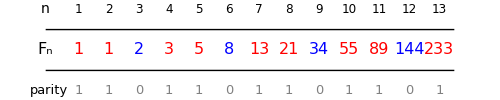

```mathematica
Graphics[Join[With[{f=Fibonacci@#},
{Text[Style[#,FontSize->12],{#,1}],
Text[Style[f,FontSize->16,FontFamily->"Cascadia Code",
If[OddQ@f,Red,Blue]],{#,0}],
Text[Style[f~Mod~2,FontSize->13,Gray],{#,-1}]}]&/@Range@13,
{Text[Style[n,FontFamily->"Times",FontSize->14],{-.1,1}],
Text[Style["F_n",FontFamily->"Times",FontSize->16],{-.1,0}],
Text[Style["parity",FontFamily->"Times",FontSize->13],{0,-1}],
Thin,Line[{{-.1,-.5},{13.5,-.5}}],Line[{{-.1,.5},{13.5,.5}}]}],ImageSize->500]
```

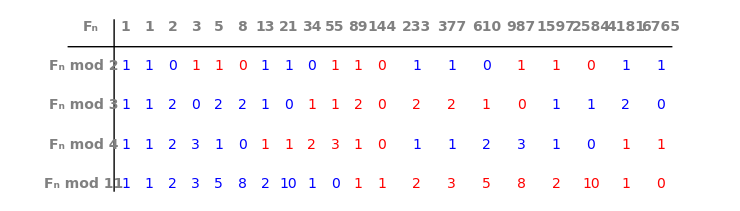

```mathematica
With[{r={2,3,4,11},f=Fibonacci@Range@20,
t1=Sequence[FontSize->14,FontFamily->"Times",Bold,Gray],
t2=Sequence[FontSize->14,FontFamily->"Cascadia Code"],
c=If[#2~Quotient~#//OddQ,Red,Blue]&,
i=#[[1]]+Ramp[#[[1]]-12].5&},
Graphics[Join[
MapIndexed[Text[Style[#,t2,Bold,Gray],{i[#2],0}]&,f],
MapIndexed[Text[Style[#~Mod~2,t2,c[3,#2[[1]]-1]],{i[#2],-1}]&,f],
MapIndexed[Text[Style[#~Mod~3,t2,c[8,#2[[1]]-1]],{i[#2],-2}]&,f],
MapIndexed[Text[Style[#~Mod~4,t2,c[6,#2[[1]]-1]],{i[#2],-3}]&,f],
MapIndexed[Text[Style[#~Mod~11,t2,c[10,#2[[1]]-1]],{i[#2],-4}]&,f],
MapIndexed[Text[Style["F_n mod "<>ToString@#,t1],-{.8,First@#2}]&,r],
{Text[Style["F_n",t1],-{.5,0}],Thin,Line[{{-1.5,-.5},{24.5,-.5}}],Line[{{.5,.2},{.5,-4.2}}]}
],ImageSize->740,AspectRatio->2/7]]
```

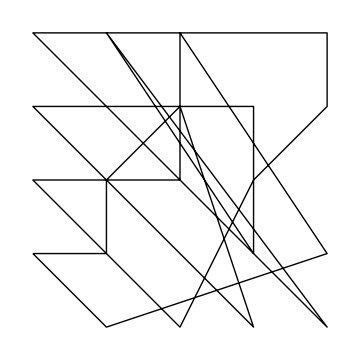
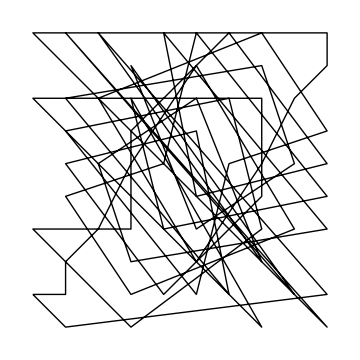

```mathematica
cobweb[modulo_, period_] := Graphics[{Thick, With[{len = period + 2},
    Line[Partition[Array[Fibonacci@#~Mod~modulo &, len, 0], 2, 1],
     VertexColors -> Array[Hue[#/len] &, period + 1, 0]]]},
     ImageSize -> Medium]
Row@{cobweb[5, 20], cobweb[10, 60]}
```

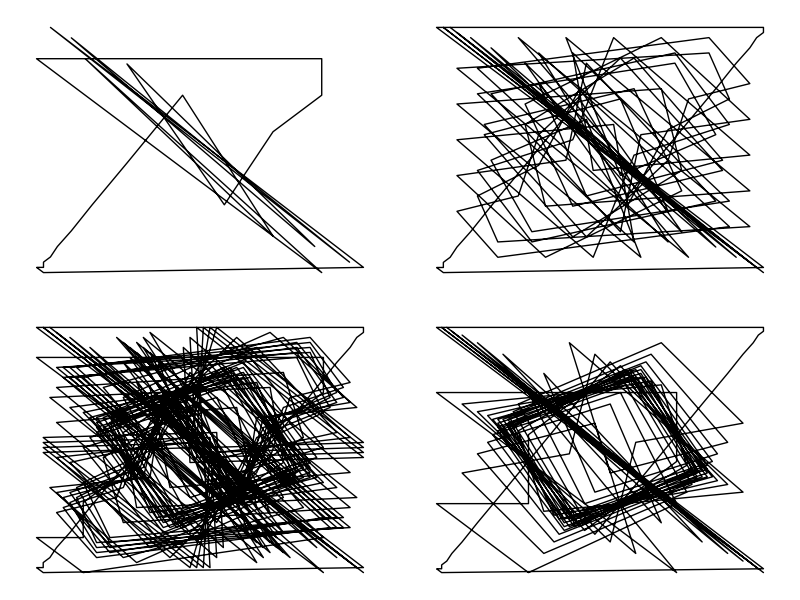

```mathematica
Grid@Partition[cobweb@@@{{48,24},{49,112},{50,300},{65,140}},2]
```

```mathematica
Manipulate[m=Min[{m,w}];ArrayPlot[Partition[Mod[Fibonacci[#]&/@Range[0,-1+w ^2 ],m]/If[h===Hue,m,m-1],w],ImageSize->400,ColorFunction->h, ColorFunctionScaling->False,AspectRatio->1],{{w,32,"carpet size"},2,64,1,Appearance->"Labeled"},
{{m,6, "modulus m"},2,w,1,Appearance->"Labeled"},{{h,"BrightBands",""},{"BrightBands"->"color",GrayLevel->"gray-level"},ControlType->SetterBar},
LabelStyle->Medium]
```